```mathematica
ClearAll["Global`*"]
```

```mathematica
(*eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred[M],bPred2->bPred[ϕ*M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*b1*P)*C1/.{k->kRes,λ1->λ[M],μ1->μ[M],σ1->σ[M],b1->b[M]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*b2*P)*C2/.{k->kRes,λ2->λ[ϕ*M],μ2->μ[ϕ*M],σ2->σ[ϕ*M],b2->b[ϕ*M]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ[M],Y1->Y[M],λ2->λ[ϕ*M],Y2->Y[ϕ*M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];*)



eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred1[M],bPred2->bPred2[M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*bmort1*P)*C1/.{k->kRes,λ1->λ1[M],μ1->μ1[M],σ1->σ1[M],bmort1->bmort1[M]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*bmort2*P)*C2/.{k->kRes,λ2->λ2[M],μ2->μ2[M],σ2->σ2[M],bmort2->bmort2[M]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ1[M],Y1->Y1[M],λ2->λ2[M],Y2->Y2[M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_preypersp.m"}],LVSS]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_preypersp.m

```mathematica
LVSS = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_preypersp.m"}]];
```

```mathematica
Length[LVSS]
```

14

```mathematica
(*Internal Fixed Point*)
Psol = P/.LVSS[[13]]
C1sol = C1/.LVSS[[13]]
C2sol=C2/.LVSS[[13]]
Rsol = R/.LVSS[[13]]
(*Boundary Fixed Points*)
PsolC1only = P/.LVSS[[10]];
C1solC1only = C1/.LVSS[[10]];
C2solC1only=C2/.LVSS[[10]];
RsolC1only = R/.LVSS[[10]];

PsolC2only = P/.LVSS[[12]];
C1solC2only = C1/.LVSS[[12]];
C2solC2only=C2/.LVSS[[12]];
RsolC2only = R/.LVSS[[12]];
```

(kRes (-1+w) bmort2[M] (-σ1[M] (2 λ1[M] (λ2[M]-2 μ2[M])+λ2[M] (2 μ1[M]+3 σ1[M]))+λ1[M] (2 λ1[M]-2 μ1[M]+3 σ1[M]) σ2[M])+kRes w bmort1[M] (2 λ2[M] (-λ2[M]+μ2[M]) σ1[M]+(2 λ1[M] (λ2[M]+μ2[M])-λ2[M] (4 μ1[M]+3 σ1[M])) σ2[M]+3 λ1[M] σ2[M]^2)+λ2[M] σ1[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))-λ1[M] σ2[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2)))/(4 kRes ((-1+w) bmort2[M] λ1[M]+w bmort1[M] λ2[M]) ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]))

(Y1[M] ((-1+w)^2 bmort2[M]^2 (4 λ2[M] μPred[M] σ1[M]^2+kRes (-1+w) α bPred2[M] Y2[M] (-2 (λ1[M]-μ1[M])^2+(λ1[M]-3 μ1[M]) σ1[M]))+(-1+w) bmort2[M] (w bmort1[M] (8 λ2[M] μPred[M] σ1[M] σ2[M]+kRes (-1+w) α bPred2[M] Y2[M] (-4 μ1[M] μ2[M]-3 μ2[M] σ1[M]+λ2[M] (4 μ1[M]+σ1[M])-3 μ1[M] σ2[M]+λ1[M] (-4 λ2[M]+4 μ2[M]+σ2[M])))+(-1+w) α bPred2[M] Y2[M] (λ1[M]-μ1[M]) √(kRes^2 ((-1+w)^2 bmort2[M]^2 (4 λ1[M]^2-4 λ1[M] (2 μ1[M]+σ1[M])+(2 μ1[M]+3 σ1[M])^2)+w^2 bmort1[M]^2 (4 λ2[M]^2-4 λ2[M] (2 μ2[M]+σ2[M])+(2 μ2[M]+3 σ2[M])^2)+2 (-1+w) w bmort1[M] bmort2[M] (-2 λ2[M] (2 μ1[M]+σ1[M])+(2 μ1[M]+3 σ1[M]) (2 μ2[M]+3 σ2[M])+λ1[M] (4 λ2[M]-2 (2 μ2[M]+σ2[M]))))))+w bmort1[M] (w bmort1[M] (4 λ2[M] μPred[M] σ2[M]^2+kRes (-1+w) α bPred2[M] Y2[M] (-2 (λ2[M]-μ2[M])^2+(λ2[M]-3 μ2[M]) σ2[M]))+(-1+w) α bPred2[M] Y2[M] (λ2[M]-μ2[M]) √(kRes^2 ((-1+w)^2 bmort2[M]^2 (4 λ1[M]^2-4 λ1[M] (2 μ1[M]+σ1[M])+(2 μ1[M]+3 σ1[M])^2)+w^2 bmort1[M]^2 (4 λ2[M]^2-4 λ2[M] (2 μ2[M]+σ2[M])+(2 μ2[M]+3 σ2[M])^2)+2 (-1+w) w bmort1[M] bmort2[M] (-2 λ2[M] (2 μ1[M]+σ1[M])+(2 μ1[M]+3 σ1[M]) (2 μ2[M]+3 σ2[M])+λ1[M] (4 λ2[M]-2 (2 μ2[M]+σ2[M]))))))))/(4 ((-1+w) bPred2[M] Y2[M] λ1[M]+w bPred1[M] Y1[M] λ2[M]) ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M])^2)

(Y2[M] (-4 λ1[M] μPred[M] ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M])^2-w α bmort2[M] bPred1[M] Y1[M] λ1[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))+w^2 α bmort2[M] bPred1[M] Y1[M] λ1[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))+w^2 α bmort1[M] bPred1[M] Y1[M] λ2[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))+w α bmort2[M] bPred1[M] Y1[M] μ1[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))-w^2 α bmort2[M] bPred1[M] Y1[M] μ1[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))-w^2 α bmort1[M] bPred1[M] Y1[M] μ2[M] √(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2))+kRes w α bPred1[M] Y1[M] ((-1+w)^2 bmort2[M]^2 (-2 (λ1[M]-μ1[M])^2+(λ1[M]-3 μ1[M]) σ1[M])+w^2 bmort1[M]^2 (-2 (λ2[M]-μ2[M])^2+(λ2[M]-3 μ2[M]) σ2[M])+(-1+w) w bmort1[M] bmort2[M] (-4 μ1[M] μ2[M]-3 μ2[M] σ1[M]+λ2[M] (4 μ1[M]+σ1[M])-3 μ1[M] σ2[M]+λ1[M] (-4 λ2[M]+4 μ2[M]+σ2[M])))))/(4 ((-1+w) bPred2[M] Y2[M] λ1[M]+w bPred1[M] Y1[M] λ2[M]) ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M])^2)

1/(4 (-1+w) bmort2[M] σ1[M]+4 w bmort1[M] σ2[M])(-kRes (-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])+kRes w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M])+√(kRes^2 (8 ((-1+w) bmort2[M] σ1[M]+w bmort1[M] σ2[M]) ((-1+w) bmort2[M] (μ1[M]+σ1[M])+w bmort1[M] (μ2[M]+σ2[M]))+((-1+w) bmort2[M] (2 λ1[M]-2 μ1[M]-σ1[M])-w bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M]))^2)))

What are the solutions if the predator is specializing on C1? (w->1)

```mathematica
PsolNoC2= FullSimplify[Psol/.w->1]
C1solNoC2= FullSimplify[C1sol/.w->1]
C2solNoC2= FullSimplify[C2sol/.w->1]
RsolNoC2 = FullSimplify[Rsol/.w->1]
```

1/(4 kRes bmort1[M]^2 λ2[M] σ2[M])(kRes bmort1[M] (2 λ2[M] (-λ2[M]+μ2[M]) σ1[M]+(2 λ1[M] (λ2[M]+μ2[M])-λ2[M] (4 μ1[M]+3 σ1[M])) σ2[M]+3 λ1[M] σ2[M]^2)+(λ2[M] σ1[M]-λ1[M] σ2[M]) √(kRes^2 bmort1[M]^2 (4 λ2[M]^2-4 λ2[M] (2 μ2[M]+σ2[M])+(2 μ2[M]+3 σ2[M])^2)))

μPred[M]/bPred1[M]

1/(4 bmort1[M] bPred1[M] Y1[M] λ2[M] σ2[M]^2)Y2[M] (α bPred1[M] Y1[M] (λ2[M]-μ2[M]) √(kRes^2 bmort1[M]^2 (4 λ2[M]^2-4 λ2[M] (2 μ2[M]+σ2[M])+(2 μ2[M]+3 σ2[M])^2))+bmort1[M] (-4 λ1[M] μPred[M] σ2[M]^2+kRes α bPred1[M] Y1[M] (-2 (λ2[M]-μ2[M])^2+(λ2[M]-3 μ2[M]) σ2[M])))

(kRes bmort1[M] (-2 λ2[M]+2 μ2[M]+σ2[M])+√(kRes^2 bmort1[M]^2 (8 σ2[M] (μ2[M]+σ2[M])+(-2 λ2[M]+2 μ2[M]+σ2[M])^2)))/(4 bmort1[M] σ2[M])

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C1],D[eqnP,C2],D[eqnP,R]},
{D[eqnC1,P],D[eqnC1,C1],D[eqnC1,C2],D[eqnC1,R]},
{D[eqnC2,P],D[eqnC2,C1],D[eqnC2,C2],D[eqnC2,R]},
{D[eqnR,P],D[eqnR,C1],D[eqnR,C2],D[eqnR,R]}})/.{P->Psol,C1->C1sol,C2->C2sol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/allometric_functions_preypersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/ppmr_primary.nb"}]];
```

Plot PPMR ~ Exp{Pred|Prey}

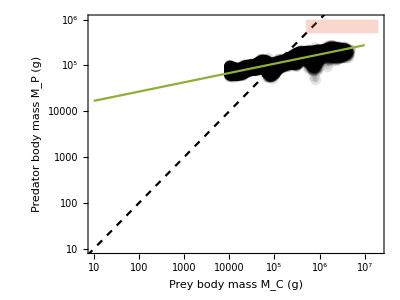

```mathematica
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[ExpPredmassdata*1000,Frame->True,FrameLabel->{"Prey body mass M_C (g)","Predator body mass M_P (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^1,2*10^7},{10^1,10^6}}],
LogLogPlot[M,{M,1,2*10^7},PlotStyle->Directive[Dashed,Black]],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
(*Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]],*)
(*LogLogPlot[Exp[4]*M,{M,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4]
```

```mathematica
PercentGrowthConsumer1=0.8; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.9; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
C2DensityList=ParallelTable[{10^i,((1/(ϕ*M))*C2sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2})/.M->10^i},{i,1,8,0.01}];
C2DensityListConsMass = Transpose[{ ϕ*C2DensityList[[All,1]],C2DensityList[[All,2]]}];
PDensityList = ParallelTable[{10^i,((1/(OptPredMass[M]))*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2})/.M->10^i},{i,1,8,0.01}];
PDensityListConsMass = Transpose[{OptPredMass[PDensityList[[All,1]]],PDensityList[[All,2]]}];
```

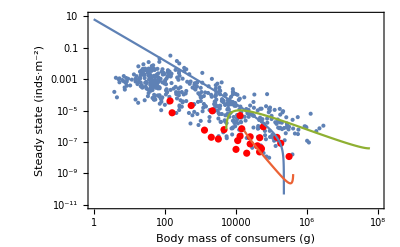

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/OptPreyMass[Mp])*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(((1/(ϕ*OptPreyMass[Mp]))*C2sol))/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],*)
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},PlotStyle->ColorData[97,1]],
ListLogLogPlot[C2DensityListConsMass/.ϕ->ScaledMassConsumer2,Joined->True,PlotStyle->ColorData[97,3]],
ListLogLogPlot[PDensityListConsMass,Joined->True,PlotStyle->ColorData[97,4]]
}]
```

```mathematica
Integrate[(1/M)*(OptPredMass[M]/M),{M,1,10^7}]
```

13262.1

A check to compare the predator mass/prey mass ratio for the Predator and Prey perspectives

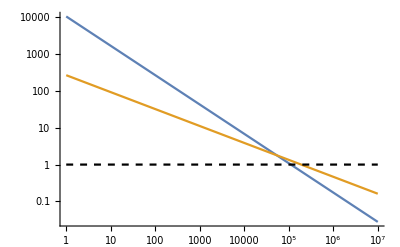

```mathematica
Show[{
LogLogPlot[(OptPredMass[M]/M),{M,1,10^7}],
LogLogPlot[(Mp/OptPreyMass[Mp]),{Mp,1,10^7},PlotStyle->ColorData[97,2]],
LogLogPlot[1,{M,1,10^7},PlotStyle->Directive[{Dashed,Black}]]
}]
```